```mathematica
results = {{1,53320},{6,3615973},{11,10442776},{16,96761768},{21,195704641},{26,281244045},{31,380604757},{36,491125737},{41,573375881},{46,667694786},{51,764730324}}
```

{{1,53320},{6,3615973},{11,10442776},{16,96761768},{21,195704641},{26,281244045},{31,380604757},{36,491125737},{41,573375881},{46,667694786},{51,764730324}}

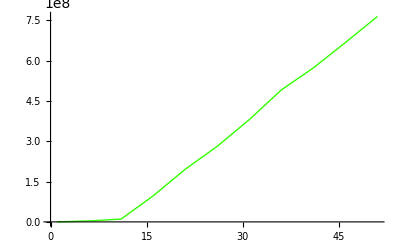

```mathematica
{{1,53320},{6,3615973},{11,10442776},{16,96761768},{21,195704641},{26,281244045},{31,380604757},{36,491125737},{41,573375881},{46,667694786},{51,764730324}}
g1 =ListLinePlot[results,PlotStyle->Hue[.3]]
```

{{1,53320},{6,3615973},{11,10442776},{16,96761768},{21,195704641},{26,281244045},{31,380604757},{36,491125737},{41,573375881},{46,667694786},{51,764730324}}

1.8×10^7

2.05×10^8

-1.6×10^7

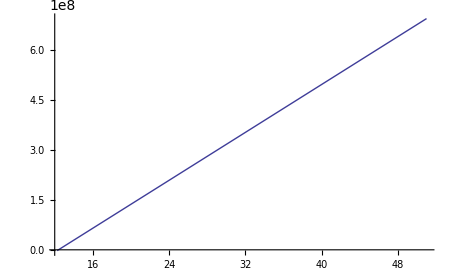

```mathematica
{{1,53320},{6,3615973},{11,10442776},{16,96761768},{21,195704641},{26,281244045},{31,380604757},{36,491125737},{41,573375881},{46,667694786},{51,764730324}}
eating = 1.8*10^7
thinking = 2.05*10^8
h[M_] := 0/; (eating*(M-1)-thinking) 
h[M_] := eating * (M - 1) - thinking/; (eating*(M-1)-thinking) > 0 
h[11.5]
g2 = Plot[h[m],{m,12.25,51}]
```

```mathematica
1.5*^7
```

1.5×10^7

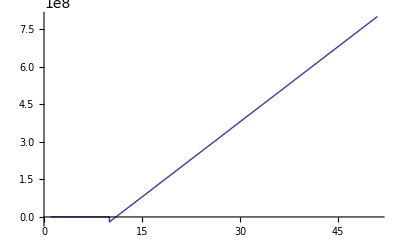

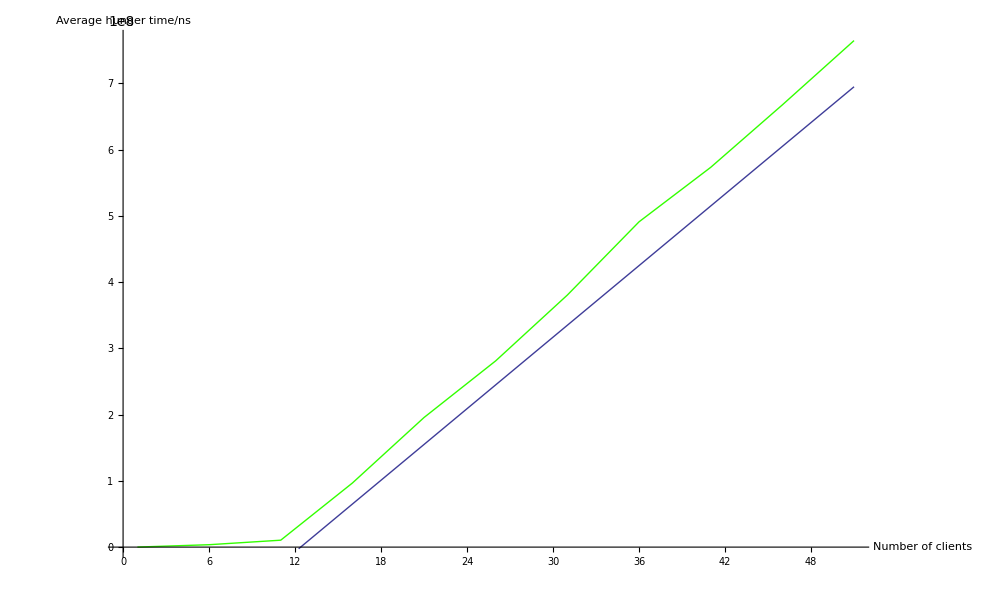

```mathematica
G= Show[g1,g2,AxesLabel->{"Number of clients","Average hunger time/ns"}]
```